```mathematica
LaunchKernels[4]
```

```mathematica
Clear[leads,LEFT,β]
```

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->-t]
```

```mathematica
T[t_,m_]:=T[t,m]=t*IdentityMatrix[m]
```

```mathematica
leads[y_]:=leads[y]=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_"<>ToString[y]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[0,2.49,0.01]}]
```

```mathematica
leads[10]
```

{{{0.-0.848911 ⅈ,-0.499585+0. ⅈ,0.+0.170328 ⅈ,-0.00145614+0. ⅈ,0.+0.0215636 ⅈ,0.00305462+0. ⅈ,0.+0.0108578 ⅈ,-0.00416569+0. ⅈ,0.-0.000257949 ⅈ,0.00451733+0. ⅈ},8,{0.00451733+0. ⅈ,0.-0.000257949 ⅈ,-0.00416569+0. ⅈ,0.+0.0108578 ⅈ,0.00305462+0. ⅈ,0.+0.0215636 ⅈ,-0.00145614+0. ⅈ,0.+0.170328 ⅈ,-0.499585+0. ⅈ,0.-0.848911 ⅈ}},248,{{0.497586-0.230577 ⅈ,8,-0.0119669+1},8,{1}}}
 |  |  |  |

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=leads[m][[Round[ω*100+1]]]
```

```mathematica
Clear[dist,list]
```

```mathematica
list[up_,down_]:=Join[Transpose[Join[{Range[1,50]},{RandomSample[Join[Table[0,50-down-up],Table[RandomInteger[{1,25}],up],Table[RandomInteger[{26,50}],down]]]}]]](*,Transpose[Join[{Range[21,40]},{RandomSample[Join[Table[0,20-down],Table[RandomInteger[{21,40}],down]]]}]]]*)
```

```mathematica
dist[up_,down_]:=dist[up,down]=ParallelTable[list[up,down],5000]
```

```mathematica
Clear[dist,list]
```

```mathematica
list[up_,down_]:=Join[Transpose[Join[{Range[1,50]},{RandomSample[Join[Table[0,40-down-up],Table[RandomInteger[{1,12}],up],Table[RandomInteger[{13,25}],down],Table[RandomInteger[{26,50}],10]]]}]]](*,Transpose[Join[{Range[21,40]},{RandomSample[Join[Table[0,20-down],Table[RandomInteger[{21,40}],down]]]}]]]*)
```

```mathematica
dist[up_,down_]:=dist[up,down]=Table[list[up,down],5000]
```

```mathematica
TLD[t_]:=Module[{sizeoflead=10},Module[{mat=RandomInteger[0,{50,50}]},ReplacePart[mat,Table[{a,a},{a,sizeoflead}]->t]]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ,50]]
```

```mathematica
SLLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=LEFT[ω,m];MAT]
```

```mathematica
device1[ω_]:=(*Module[{sizeoflead=50},*)Inverse[IdentityMatrix[50]-g[ω,0.0001,1,0].TLD[1].SLLEAD[ω,10].TLD[1]].g[ω,0.0001,1,0]
```

```mathematica
device1[1][[1,1]]
```

0.376543-0.675031 ⅈ

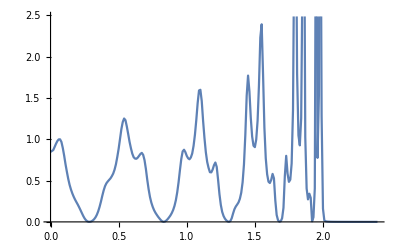

```mathematica
ListLinePlot[Table[{ω,-Im[device1[ω][[40,40]]]},{ω,Range[0,2.4,0.01]}]]
```

```mathematica
CA[ω_,ϵ1_,up_,down_,number_]:= Module[{sizeoflead=10},
recurs=Module[{J= device1[ω]},
Do[
J=Inverse[IdentityMatrix[50]-Inverse[Module[{κ=β[ω,0.0001,1,0,50],n= dist[up,down][[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*0.0001-ϵ1]]].T[1,50].J.T[1,50]].Inverse[Module[{κ=β[ω,0.0001,1,0,50],n= dist[up,down][[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*0.0001-ϵ1]]],{loc1,50}];J=J];ir=Inverse[IdentityMatrix[50]-SLLEAD[ω,sizeoflead].TLD[1].recurs.TLD[1]].SLLEAD[ω,sizeoflead];il=Inverse[IdentityMatrix[50]-recurs.TLD[1].SLLEAD[ω,sizeoflead].TLD[1]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TLD[1].recurs;
(*Gnonlocallr=recurs.ConjugateTranspose[TLD[1]].ir;*)
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TLD[1].grr1.TLD[1]-TLD[1].GNON1.TLD[1].GNON1]];TRA]
```

```mathematica
CA[0,0,10,10,1]
```

0.359089

```mathematica
input =Table[ParallelTable[{ω,CA[ω,1,20,20,num]},{ω,Range[0,2.4,0.01]}],{num,50}]
```

{{{0.,5.00808},{0.01,1.87509},{0.02,2.39613},{0.03,5.06188},{0.04,3.52311},{0.05,4.55562},{0.06,8.32971},{0.07,1.91939},{0.08,5.09012},{0.09,22.6092},{0.1,6.21884},{0.11,7.96672},217,{2.29,0.72577},{2.3,1.69425},{2.31,1.0115},{2.32,0.702193},{2.33,0.222704},{2.34,0.847317},{2.35,0.634407},{2.36,0.531201},{2.37,1.12415},{2.38,1.0613},{2.39,1.0385},{2.4,1.32398}},48,{1}}
 |  |  |  |

```mathematica
CA[1,1,10,10,2]
```

2.34289

```mathematica
fff[up_,down_]:=Export["/home/shardulfwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/50imp/top_"<>ToString[up]<>"_bot_"<>ToString[down]<>"_ϵ1.dat",Table[{ω,Mean[ParallelTable[CA[ω,1,up,down,NUM],{NUM,500}]]},{ω,Range[0,2,0.01]}]]
```

```mathematica
Table[Print[x];fff[x,50-x],{x,0,50,5}]
```

{/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_25_size_5050/50imp/top_0_bot_50_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_25_size_5050/50imp/top_5_bot_45_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_25_size_5050/50imp/top_10_bot_40_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_25_size_5050/50imp/top_15_bot_35_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_25_size_5050/50imp/top_20_bot_30_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_25_size_5050/50imp/top_25_bot_25_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_25_size_5050/50imp/top_30_bot_20_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_25_size_5050/50imp/top_35_bot_15_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_25_size_5050/50imp/top_40_bot_10_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_25_size_5050/50imp/top_45_bot_5_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_25_size_5050/50imp/top_50_bot_0_.dat}

```mathematica
ggg[total_,up_,down_]:=Export["/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/"<>ToString[total]<>"imp/top_"<>ToString[up]<>"_bot_"<>ToString[down]<>"_ϵ1_10_lower.dat",Table[{ω,Mean[ParallelTable[CA[ω,1,up,down,NUM],{NUM,500}]]},{ω,Range[0,2,0.01]}]]
```

```mathematica
ggg[40,20,20]
```

/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/40imp/top_20_bot_20_ϵ1_10_lower.dat

```mathematica
Table[ggg[40,x,40-x],{x,Range[0,40,2]}]
```

{/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/40imp/top_0_bot_40_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/40imp/top_2_bot_38_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/40imp/top_4_bot_36_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/40imp/top_6_bot_34_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/40imp/top_8_bot_32_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/40imp/top_10_bot_30_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/40imp/top_12_bot_28_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/40imp/top_14_bot_26_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/40imp/top_16_bot_24_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/40imp/top_18_bot_22_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/40imp/top_20_bot_20_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/40imp/top_22_bot_18_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/40imp/top_24_bot_16_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/40imp/top_26_bot_14_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/40imp/top_28_bot_12_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/40imp/top_30_bot_10_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/40imp/top_32_bot_8_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/40imp/top_34_bot_6_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/40imp/top_36_bot_4_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/40imp/top_38_bot_2_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/40imp/top_40_bot_0_ϵ1_10_lower.dat}

```mathematica
Table[ggg[30,x,30-x],{x,Range[0,30,2]}]
```

$Aborted

```mathematica
Table[ggg[20,x,20-x],{x,Range[0,20,2]}]
```

{/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/20imp/top_0_bot_20_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/20imp/top_2_bot_18_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/20imp/top_4_bot_16_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/20imp/top_6_bot_14_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/20imp/top_8_bot_12_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/20imp/top_10_bot_10_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/20imp/top_12_bot_8_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/20imp/top_14_bot_6_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/20imp/top_16_bot_4_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/20imp/top_18_bot_2_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/20imp/top_20_bot_0_ϵ1_10_lower.dat}

```mathematica
Table[ggg[20,x,20-x],{x,Range[0,10,2]}]
```

{/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/20imp/top_0_bot_20_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/20imp/top_2_bot_18_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/20imp/top_4_bot_16_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/20imp/top_6_bot_14_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/20imp/top_8_bot_12_ϵ1_10_lower.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/20imp/top_10_bot_10_ϵ1_10_lower.dat}

```mathematica
Table[Print[t];Table[ggg[40,x,40-x],{x,Range[0,40,2]}],{t,Range[10,40,10]}]
```

10

20

30

40

50

{{/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/10imp/top_0_bot_10_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/10imp/top_5_bot_5_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/10imp/top_10_bot_0_ϵ1.dat},{/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/20imp/top_0_bot_20_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/20imp/top_5_bot_15_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/20imp/top_10_bot_10_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/20imp/top_15_bot_5_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/20imp/top_20_bot_0_ϵ1.dat},{/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/30imp/top_0_bot_30_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/30imp/top_5_bot_25_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/30imp/top_10_bot_20_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/30imp/top_15_bot_15_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/30imp/top_20_bot_10_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/30imp/top_25_bot_5_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/30imp/top_30_bot_0_ϵ1.dat},{/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/40imp/top_0_bot_40_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/40imp/top_5_bot_35_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/40imp/top_10_bot_30_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/40imp/top_15_bot_25_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/40imp/top_20_bot_20_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/40imp/top_25_bot_15_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/40imp/top_30_bot_10_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/40imp/top_35_bot_5_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/40imp/top_40_bot_0_ϵ1.dat},{/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/50imp/top_0_bot_50_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/50imp/top_5_bot_45_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/50imp/top_10_bot_40_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/50imp/top_15_bot_35_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/50imp/top_20_bot_30_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/50imp/top_25_bot_25_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/50imp/top_30_bot_20_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/50imp/top_35_bot_15_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/50imp/top_40_bot_10_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/50imp/top_45_bot_5_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_10_size_5050epsi1/50imp/top_50_bot_0_ϵ1.dat}}

```mathematica
transmission = Table[{x,Import["/homRange[0,40,2]}]
```

{{0,{{0.,2.78971},{0.01,2.36127},{0.02,2.21599},{0.03,2.28499},{0.04,1.98916},{0.05,2.32614},{0.06,2.70515},{0.07,3.29979},{0.08,6.28232},{0.09,2.80767},{0.1,1.48006},{0.11,0.968119},178,{1.9,2.12748},{1.91,2.2413},{1.92,2.30316},{1.93,2.26104},{1.94,2.19191},{1.95,2.13282},{1.96,2.17801},{1.97,2.21833},{1.98,2.24453},{1.99,2.28875},{2.,2.2386}}},19,{40,{1}}}
 |  |  |  |

```mathematica
Dimensions[transmission]
```

{21,2}

```mathematica
misfit[x_,y_,n_]:=Module[{m5=input[[n]]},
ρ1=Table[{transmission[[con,1]]+0.2,Module[{B1=Transpose[{m5[[1;;201]][[;;,1]],(m5[[1;;201,2]]-transmission[[con,2]][[1;;201,;;]][[;;,2]])^2}]},NIntegrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]},{con,21}];lista=ρ1(*,ρ2,ρ3,ρ4*)(*,ρ5,ρ6*);
{lista,lista[[Position[lista,Min[lista]][[1,1]]]]}]
```

```mathematica
ListLinePlot[]
```

```mathematica
misfit[2,0.5,2][[2]]
```

{10.2,0.0027435}

```mathematica
Table[Abs[misfit[2,0.5,n][[2]][[1]]-20.2]/20.2,{n,50}]//Mean
```

0.239604

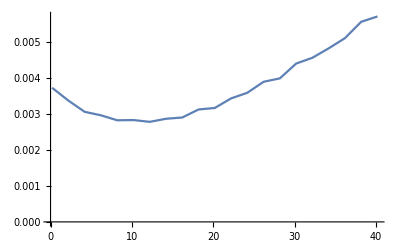

```mathematica
ListLinePlot[misfit[2,0.5,1][[1]]]
```

```mathematica
dist[10,30][[27]]
```

{{1,25},{2,15},{3,15},{4,16},{5,14},{6,14},{7,3},{8,8},{9,21},{10,42},{11,44},{12,21},{13,10},{14,22},{15,41},{16,17},{17,24},{18,20},{19,10},{20,17},{21,24},{22,7},{23,15},{24,3},{25,13},{26,13},{27,19},{28,22},{29,19},{30,19},{31,22},{32,23},{33,3},{34,33},{35,35},{36,14},{37,13},{38,37},{39,50},{40,18},{41,23},{42,35},{43,9},{44,1},{45,34},{46,6},{47,47},{48,15},{49,18},{50,13}}

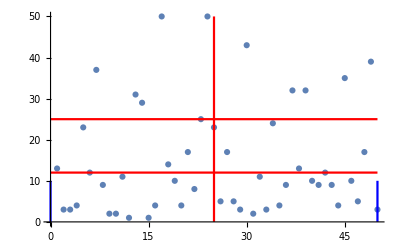

```mathematica
Show[ListPlot[dist[30,10][[30]]],ListLinePlot[Table[{x,25},{x,0,50}],PlotStyle->Red],ListLinePlot[Table[{25,x},{x,0,50}],PlotStyle->Red],ListLinePlot[Table[{x,12},{x,0,50}],PlotStyle->Red],(*ListLinePlot[Table[{x,15},{x,0,50}],PlotStyle->Red],*)ListLinePlot[Table[{0,y},{y,0,10}],PlotStyle->Blue],ListLinePlot[Table[{50,y},{y,0,10}],PlotStyle->Blue]]
```

```mathematica
Import["/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_20_size_5050_epsi1_leadright/40_top_10_.dat"]
```

{{0.,5.46225},{0.02,7.70385},{0.04,5.02504},{0.06,6.30611},{0.08,5.40245},{0.1,5.6978},{0.12,8.65665},{0.14,9.4462},{0.16,9.60092},{0.18,9.21837},{0.2,6.1801},{0.22,9.40742},{0.24,10.2789},{0.26,10.749},{0.28,11.0928},{0.3,10.9233},{0.32,10.4189},{0.34,9.64844},{0.36,9.20154},{0.38,10.1687},{0.4,11.043},{0.42,11.294},{0.44,11.3469},{0.46,11.201},{0.48,11.3144},{0.5,11.0626},{0.52,10.3418},{0.54,8.95438},{0.56,10.3714},{0.58,10.8324},{0.6,10.9737},{0.62,10.953},{0.64,11.2328},{0.66,11.3204},{0.68,11.261},{0.7,11.007},{0.72,10.6691},{0.74,10.2865},{0.76,9.33425},{0.78,10.1324},{0.8,10.1955},{0.82,10.6099},{0.84,10.8445},{0.86,10.9613},{0.88,10.9582},{0.9,10.7835},{0.92,10.7388},{0.94,10.7714},{0.96,10.6485},{0.98,10.2569},{1.,8.15767},{1.02,9.28523},{1.04,9.93846},{1.06,10.2048},{1.08,10.3081},{1.1,10.3102},{1.12,10.1594},{1.14,10.3103},{1.16,10.4056},{1.18,10.4179},{1.2,10.3007},{1.22,10.0264},{1.24,9.64743},{1.26,9.34598},{1.28,8.82209},{1.3,9.27907},{1.32,9.45415},{1.34,9.41397},{1.36,9.53996},{1.38,9.73319},{1.4,9.78815},{1.42,9.82051},{1.44,9.76461},{1.46,9.47904},{1.48,9.49573},{1.5,9.55025},{1.52,9.42443},{1.54,9.05322},{1.56,7.94386},{1.58,8.19526},{1.6,8.64629},{1.62,8.89606},{1.64,8.99536},{1.66,9.09588},{1.68,9.03888},{1.7,8.89672},{1.72,8.92379},{1.74,9.02797},{1.76,9.00064},{1.78,8.96571},{1.8,8.80458},{1.82,8.44066},{1.84,8.00069},{1.86,7.61062},{1.88,7.94022},{1.9,8.0573},{1.92,8.13252},{1.94,8.05201},{1.96,8.03942},{1.98,8.27319},{2.,8.30263}}

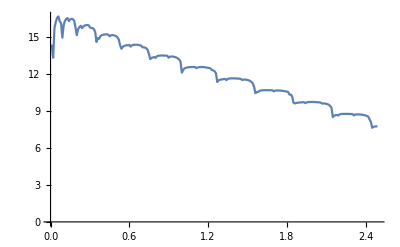

```mathematica
ListPlot[%113,Joined->True]
```